{0,0,10,12,30,24,20,18,19,15,0,0,0,2}

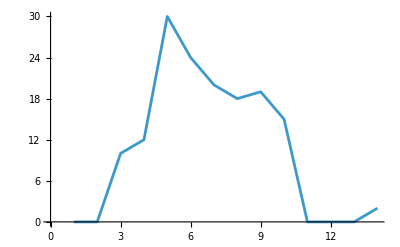

```mathematica
l1={0,0,10,12,30,24,20,18,19,15,0,0,0,2}
ListLinePlot[l1]
```

```mathematica
cwt=ContinuousWaveletTransform[l1,MexicanHatWavelet[1],{3,4}]
```

ContinuousWaveletData[…]

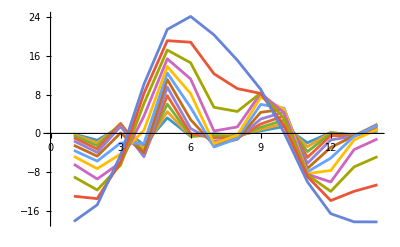

```mathematica
ListLinePlot[cwt[All,"Values"]]
```

```mathematica
cwt[All,"Values"]//Dimensions
```

{12,14}

```mathematica
tmp=ContinuousWaveletTransform[l1,MexicanHatWavelet[0.5],{3,4}]
```

ContinuousWaveletData[…]

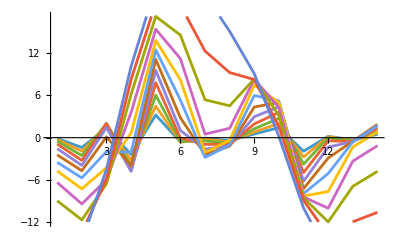

```mathematica
ListLinePlot[tmp[All,"Values"],PlotRange->Full]
```

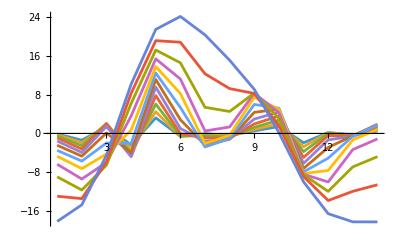

```mathematica
ListLinePlot[Map[Re,tmp[All,"Values"]],PlotRange->Full]
```

{0,0,10,12,30,40,60,100,110,111}

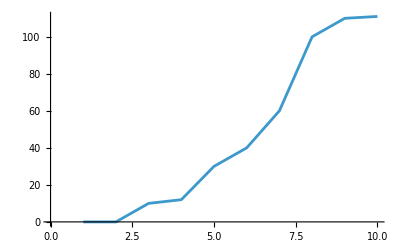

```mathematica
l2={0,0,10,12,30,40,60,100,110,111}
ListLinePlot[l2]
```

```mathematica
cwt2=ContinuousWaveletTransform[l2,MexicanHatWavelet[1],{3,4}]
```

ContinuousWaveletData[…]

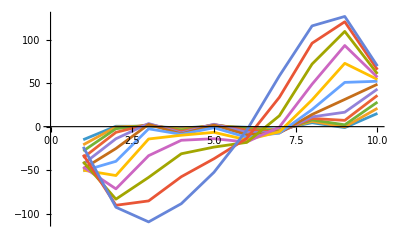

```mathematica
ListLinePlot[cwt2[All,"Values"]]
```

{0.0685395,0.971317,0.835145,0.547189,0.592368,0.373201,0.872529,0.569033,0.305654,0.983477}

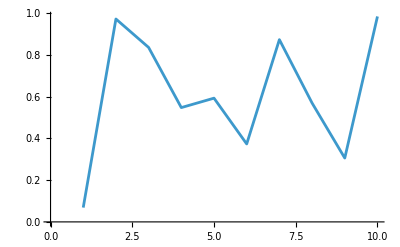

```mathematica
lr=Table[RandomReal[],{10}]
ListLinePlot[lr]
```

```mathematica
cwtr=ContinuousWaveletTransform[lr,MexicanHatWavelet[1]]
```

ContinuousWaveletData[…]

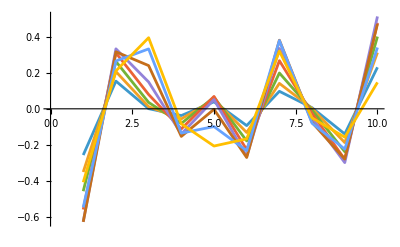

```mathematica
ListLinePlot[cwtr[All,"Values"]]
```

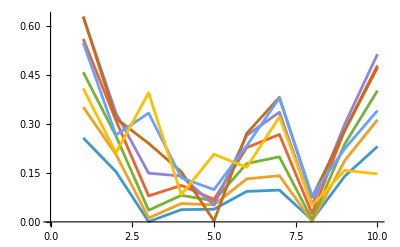

```mathematica
Map[Abs,cwtr[All,"Values"]]//ListLinePlot
```

```mathematica
Map[Norm,cwtr[All,"Values"],{-1}]//ListLinePlot
```

-Graphics-

```mathematica
Map[Re,cwtr[All,"Values"],{-1}]//ListLinePlot
```

-Graphics-

ピーク推定

モジュール読み込み：

```mathematica
Get["/Users/kouamano/gitsrc/SCRIPT_Mathematica/SCRIPTS/Wavelet.txt"]
```

```mathematica
cwtr[All,"Values"]
```

{{-0.257223-1.80019×10^-18 ⅈ,0.154039-9.75365×10^-19 ⅈ,0.000746935+8.24187×10^-18 ⅈ,-0.037502-9.25926×10^-18 ⅈ,0.0388811+2.03553×10^-18 ⅈ,-0.0933597+2.3862×10^-18 ⅈ,0.0974231+2.03553×10^-18 ⅈ,0.00595493-8.17265×10^-18 ⅈ,-0.139969+8.24187×10^-18 ⅈ,0.231009-2.73353×10^-18 ⅈ},{-0.351663-6.28519×10^-18 ⅈ,0.206998-4.81704×10^-18 ⅈ,0.0117665+1.37989×10^-17 ⅈ,-0.0561577-1.86388×10^-17 ⅈ,0.0522085+1.38627×10^-18 ⅈ,-0.131821-6.06335×10^-18 ⅈ,0.141485+1.38627×10^-18 ⅈ,0.00220625-3.57074×10^-18 ⅈ,-0.187877+1.37989×10^-17 ⅈ,0.312855+9.00467×10^-18 ⅈ},{-0.458501+1.83347×10^-19 ⅈ,0.263427+1.92456×10^-17 ⅈ,0.035592+1.64317×10^-17 ⅈ,-0.0814514-7.64411×10^-18 ⅈ,0.0646204-2.18726×10^-18 ⅈ,-0.178601-1.22817×10^-17 ⅈ,0.199242-2.18726×10^-18 ⅈ,-0.00750894-3.33994×10^-17 ⅈ,-0.23866+1.64317×10^-17 ⅈ,0.40184+5.40735×10^-18 ⅈ},{-0.560382,0.311335,0.0796354,-0.11185,0.0688141,-0.227585,0.267784,-0.0256649,-0.28116,0.479073},{-0.628159,0.33373,0.149286,-0.140512,0.0515917,-0.264958,0.335844,-0.0513297,-0.29939,0.513897},{-0.629254-1.80256×10^-17 ⅈ,0.317083+1.3723×10^-18 ⅈ,0.240585+2.21426×10^-17 ⅈ,-0.153543-1.51955×10^-17 ⅈ,-0.0029003-2.68274×10^-18 ⅈ,-0.270972+8.09542×10^-18 ⅈ,0.381593-2.68274×10^-18 ⅈ,-0.0754692-1.30223×10^-17 ⅈ,-0.27984+2.21426×10^-17 ⅈ,0.472717-2.14404×10^-18 ⅈ},{-0.548485+7.83919×10^-18 ⅈ,0.266131+1.99164×10^-17 ⅈ,0.333315+4.00347×10^-18 ⅈ,-0.135248-1.95225×10^-18 ⅈ,-0.0988416-2.20287×10^-18 ⅈ,-0.233059-9.69301×10^-18 ⅈ,0.379753-2.20287×10^-18 ⅈ,-0.0801864-3.08107×10^-17 ⅈ,-0.224427+4.00347×10^-18 ⅈ,0.34105+1.10992×10^-17 ⅈ},{-0.408598+8.15839×10^-19 ⅈ,0.21102+1.37558×10^-17 ⅈ,0.395515+8.15839×10^-19 ⅈ,-0.0833849-6.71763×10^-18 ⅈ,-0.207215+8.15839×10^-19 ⅈ,-0.167229+1.83323×10^-18 ⅈ,0.321471+8.15839×10^-19 ⅈ,-0.0509357-1.92845×10^-17 ⅈ,-0.157754+8.15839×10^-19 ⅈ,0.147111+6.33382×10^-18 ⅈ}}

```mathematica
WTPE[cwtr[All,"Values"]]
```

2

```mathematica
cwt2[All,"Values"]//WTPE
```

1

```mathematica
cwt[All,"Values"]//WTPE
```

2

```mathematica
WTPE[cwt[All,"Values"],"position"]
```

{{5},{9},{10}}

```mathematica
WTPE[cwtr[All,"Values"],"position"]
```

{{2},{3},{7}}